# Nf=2; q/T^3 VS T

```mathematica
λ2=0.2573
```

0.2573

```mathematica
A3[z_]:=(1/2) Log[2.94 Sin[1.24 Sin[0.47 z+1.94]-9.55]+3.53]
```

```mathematica
AS3[z_]:=(1/2) Log[2.94 Sin[1.24 Sin[0.47 z+1.94]-9.55]+3.53]
```

```mathematica
T3[zh_]:=1/(π zh)
```

```mathematica
g3[z_,zh_]:=1-(1/zh^4) z^4
```

```mathematica
a03[zh_]:=NIntegrate[(z^2*Exp[-2*AS3[z]])/(√(g3[z,zh](1-g3[z,zh]))),{z,0,zh}]
```

```mathematica
q3[zh_]:=λ2/(Pi*a03[zh])
```

```mathematica
qz3[zh_]:=q3[zh]/(T3[zh])^3
```

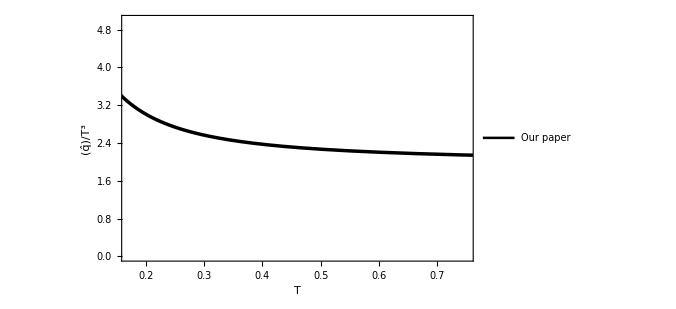

```mathematica
x3=ListLinePlot[ParallelTable[{Re[T3[zh]],Re[qz3[zh]]},{zh,0.03,3.5,0.05}],Frame->True,FrameStyle->Directive[Black,Thin,FontFamily->"Times New Roman"],PlotStyle->{{Black,Thickness[0.005]}},BaseStyle->{Black,FontSize->17},PlotLegends->Placed[LineLegend[{"Our paper"},LabelStyle->{FontSize->15}],{0.8,0.8}],FrameLabel->{Style["T",15,Black,Italic],Style[q̂/T^3,15,Black]},ImageSize->{500,300}, 
  PlotRange -> {{0.17, 0.75}, {0, 5}}]
```

# JETSCAPE

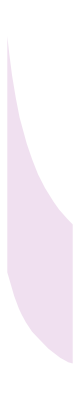

```mathematica
x4=Legended[Graphics[{LightPurple,Polygon[{{0.170,4.632},{0.170,2.008},{0.2346,1.742},{0.278,1.603},{0.303,1.539},{0.343,1.4507},{0.399,1.349},{0.469,1.2605},{0.551,1.159},{0.606,1.108},{0.660,1.058},{0.737,1.007},{0.777,0.994},{0.777,2.541},{0.726,2.604},{0.651,2.706},{0.599,2.794},{0.520,2.946},{0.455,3.0986},{0.401,3.263},{0.350,3.441},{0.2836,3.7324},{0.2486,3.948},{0.2136,4.2014},{0.189,4.430}}]}],Placed[SwatchLegend[{LightPurple},{"JETSCAPE"},LabelStyle->{FontSize->15}],{0.5,0.8}]]
```

```mathematica
Show[x3,x4,ImageSize->{500,300}]
```